# Experimental trajectories and Simulated Trajectories

## getting Diffusion Coefficient and Velocity

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\props.m";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\Brachyury_motion_2.mx";
```

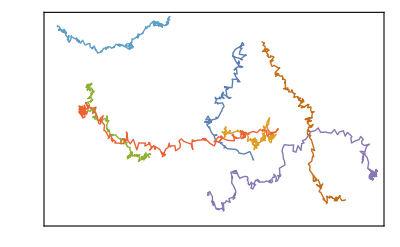

```mathematica
ListLinePlot[saved,PlotStyle->Thick,FrameTicks-> None,Frame->True]
```

```mathematica
t=6  (* min *);resolution = 0.633 (*um*); binningRatio =2;
```

```mathematica
traj=saved*resolution*binningRatio;
```

```mathematica
msds=MSD[#,30,"M2"]&/@saved;
```

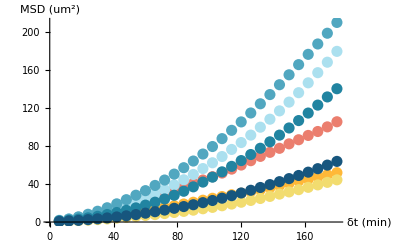

```mathematica
ListPlot[Thread[{Range@Length[#]*t,#*binningRatio*resolution^2}]&/@msds,PlotStyle->ColorData[24],AxesLabel->{Style["δt (min)",{Bold,15}],
Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14]]/.PointSize[_]:> PointSize[0.02]
```

```mathematica
χ=(Thread[{Range@Length@# *t,#*binningRatio*resolution^2}]&/@msds)[[All,1;;4]]; (*linear part of trajectories*)
```

```mathematica
(* Δ is diffusion coefficient *)
```

```mathematica
Clear[x];
Δ=Mean@TakeLargest[Map[Normal[LinearModelFit[#,x,x]]/.(_+g_ x):> g&,χ],4]/4 (* division by a factor of 4 since motion is in 2D *)
```

0.0720957

```mathematica
(* I also computed the average Diffusion Coefficient for the different trajectories using Andrew Berglund's code. 
From Berglund's code: D = 0.0691 um/min; (Close enough)
*)
```

```mathematica
σ = Sqrt[4 Δ t]; (* standard deviation *)
```

```mathematica
ν=(Mean@BlockMap[(EuclideanDistance@@#)/t&,#,2,1]&/@traj)//Mean (* ν is average velocity in um/min *)
```

0.221431

```mathematica
minFrames=(Min@*Map[Length]@saved)-1
```

98

```mathematica
avgDist=minFrames(t*ν) (* distance in um moved for the avg. # of frames recorded *)
```

130.202

## Simulated Trajectory - Pure Brownian Motion

```mathematica
cf= ColorData["Rainbow"];
```

```mathematica
SeedRandom[12345];
```

```mathematica
h=0.5;
data=Table[Transpose[RandomFunction[FractionalBrownianMotionProcess[0,σ,h],{0,(minFrames-1)t,t},2]["ValueList"]],{250}];
```

```mathematica
minmax=MinMax@data;
```

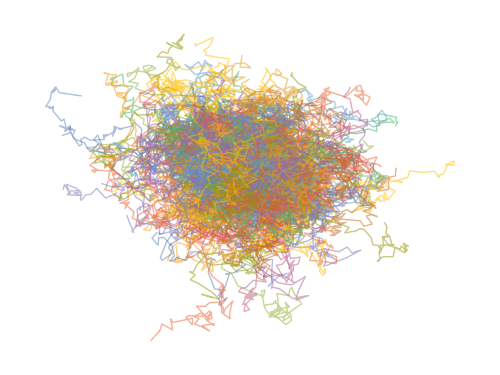

```mathematica
ListPlot[
data,Joined->True,ImageSize->500,PlotRange->All,AspectRatio->3/4,
BaseStyle->Directive[Thin,Opacity[0.5]],Axes->False,PlotStyle->Thick
]
```

```mathematica
Clear[xr,yr,sdr];
```

```mathematica
{xr,yr}=TemporalData[#,{0,(minFrames-1)*t,t}]&/@Transpose[data,{2,3,1}];
```

```mathematica
xr/:sdr[Unevaluated@xr]:=xr["SliceData",(minFrames-1)*t];
yr/:sdr[Unevaluated@yr]:=yr["SliceData",(minFrames-1)*t];
```

```mathematica
{barxr,baryr}=With[{min =Min[#],max=Max[#] },
BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,
ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{min,max},{0,1}]),
ImageSize->63]&[HistogramList[#,{Range[min,max,(max-min)/20]}]]
]&/@{sdr[Unevaluated@xr],sdr[Unevaluated@yr]}
```

{-Graphics-,-Graphics-}

```mathematica
(* x plot *)
```

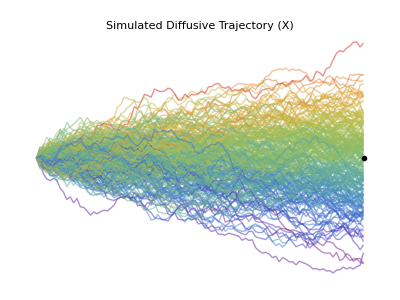

```mathematica
ListPlot[xr,PlotStyle->(cf/@Rescale[sdr[Unevaluated@xr]]),Joined->True,ImageSize->400,
PlotRange->All,AspectRatio->3/4,Epilog->Inset[barxr,{1+(minFrames-1)t,0},{0,11.0}],Axes-> None,
BaseStyle->Directive[Thick,Opacity[0.5]],PlotRangePadding->{{0,102},{.5,.5}},
PlotLabel->Style["Simulated Diffusive Trajectory (X)",{Bold,Black,FontSize->20}]]
```

```mathematica
(* compute the autocorrelation for the x coordinate of the trajectories *)
```

```mathematica
acfXr=CorrelationFunction[#,{0,Length@#-1}]&/@Part[xr,2,1];
```

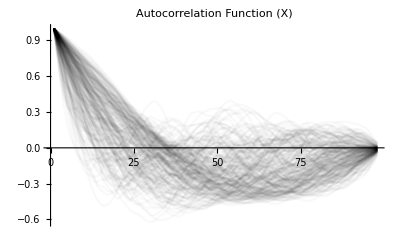

```mathematica
ListPlot[acfXr,Joined->True,PlotStyle->Directive[Opacity[0.025],Black],
PlotLabel->Style["Autocorrelation Function (X)",Bold,Black,FontSize->14],
AxesStyle-> {Thin,18},PlotRange->All]
```

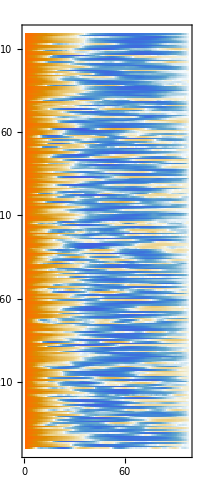

```mathematica
MatrixPlot[acfXr,FrameTicks->{Range[10,250,50],Range[0,100,20]}]
```

```mathematica
(* y plot *)
```

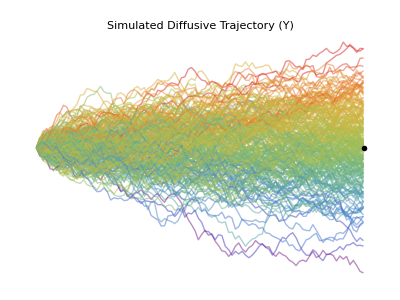

```mathematica
ListPlot[
yr,PlotStyle->(cf/@Rescale[sdr[Unevaluated@yr]]),Joined->True,ImageSize->400,PlotRange->All,AspectRatio->3/4,
Epilog->Inset[baryr,{1.0+(minFrames-1)t,0},{0,11.0}],Axes-> None,
BaseStyle->Directive[Thick,Opacity[0.5]],PlotRangePadding->{{0,102},{.5,.5}},
PlotLabel->Style["Simulated Diffusive Trajectory (Y)",{Bold,Black,FontSize->20}]
]
```

```mathematica
(* compute the autocorrelation for the y coordinate of the trajectories *)
```

```mathematica
acfYr=CorrelationFunction[#,{0,Length@#-1}]&/@Part[yr,2,1];
```

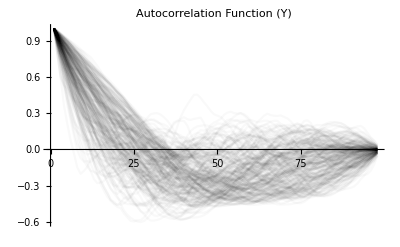

```mathematica
ListPlot[acfYr,Joined->True,PlotStyle->Directive[Opacity[0.025],Black],
PlotLabel->Style["Autocorrelation Function (Y)",Bold,Black,FontSize->14],
AxesStyle-> {Thin,18},PlotRange->All]
```

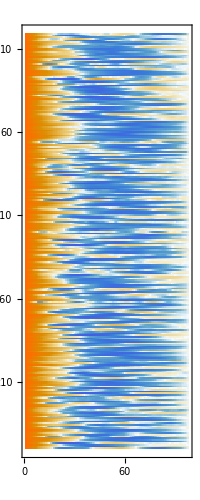

```mathematica
MatrixPlot[acfYr,FrameTicks->{Range[10,250,50],Range[0,100,20]}]
```

## Simulated Trajectory - Fractional Brownian Motion

```mathematica
(* +vely autocorrelated trajectories *)
```

```mathematica
cf= ColorData["Rainbow"];
```

```mathematica
SeedRandom[12345];
```

```mathematica
h=Block[{t1,t2},
Table[
{t1,t2}=TimeSeries[Thread[{Range@Length@#,#}]]&/@{i[[All,1]],i[[All,2]]};
Max[oo/.FindProcessParameters[#,FractionalBrownianMotionProcess[oo]]&/@{t1,t2}],{i,saved}]
]
```

{0.706414,0.567296,0.855557,0.623653,0.676964,0.573884,0.894041}

```mathematica
hurst=Max[h]
```

0.894041

```mathematica
data=Table[Transpose[RandomFunction[FractionalBrownianMotionProcess[0,σ,hurst],{0,(minFrames-1)t,t},2]["ValueList"]],{250}];
```

```mathematica
minmax=MinMax@data;
```

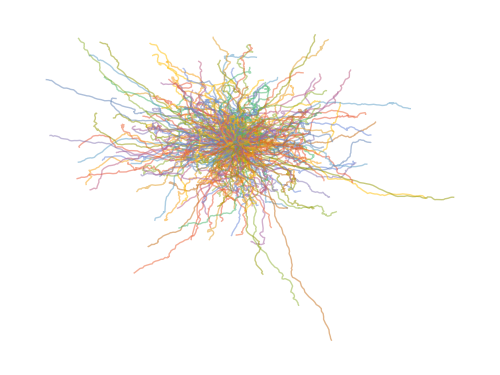

```mathematica
ListPlot[
data,Joined->True,ImageSize->500,PlotRange->All,AspectRatio->3/4,
BaseStyle->Directive[Thin,Opacity[0.5]],Axes->False,PlotStyle->Thick
]
```

```mathematica
ClearAll[x,y,sd];
```

```mathematica
{x,y}=TemporalData[#,{0,(minFrames-1)t,t}]&/@Transpose[data,{2,3,1}];
```

```mathematica
x/:sd[Unevaluated@x]:=x["SliceData",(minFrames-1)t];
y/:sd[Unevaluated@y]:=y["SliceData",(minFrames-1)t];
```

```mathematica
{barx,bary}=With[{min =Min[#],max=Max[#] },
BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,
ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{min,max},{0,1}]),
ImageSize->63]&[HistogramList[#,{Range[min,max,(max-min)/20]}]]
]&/@{sd[Unevaluated@x],sd[Unevaluated@y]}
```

{-Graphics-,-Graphics-}

```mathematica
(* x plot *)
```

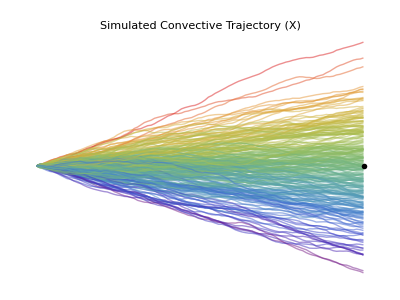

```mathematica
ListPlot[x,PlotStyle->(cf/@Rescale[sd[Unevaluated@x]]),Joined->True,ImageSize->400,PlotRange->All,
AspectRatio->3/4,Epilog->Inset[barx,{1.0+(minFrames-1)t,0},{0,10.3}],Axes-> None,
BaseStyle->Directive[Thick,Opacity[0.5]],PlotRangePadding->{{0,102},{.5,.5}},
PlotLabel->Style["Simulated Convective Trajectory (X)",{Bold,Black,FontSize->20}]
]
```

```mathematica
(* compute the autocorrelation for the x coordinate of the trajectories *)
```

```mathematica
acfX=CorrelationFunction[#,{0,Length@#-1}]&/@Part[x,2,1];
```

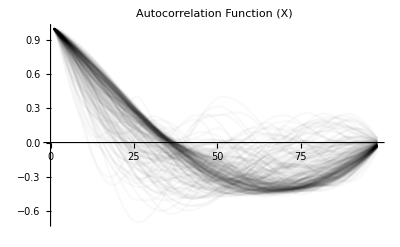

```mathematica
ListPlot[acfX,Joined->True,PlotStyle->Directive[Opacity[0.025],Black],
PlotLabel->Style["Autocorrelation Function (X)",Bold,Black,FontSize->14],
AxesStyle-> {Thin,18}]
```

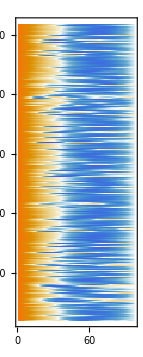

```mathematica
MatrixPlot[acfX,FrameTicks->{Range[10,250,50],Range[0,100,20]}]
```

```mathematica
(* y plot *)
```

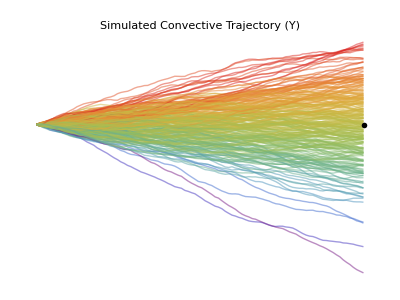

```mathematica
ListPlot[
y,PlotStyle->(cf/@Rescale[sd[Unevaluated@y]]),Joined->True,ImageSize->400,PlotRange->All,
AspectRatio->3/4,Epilog->Inset[bary,{1.0+(minFrames-1)t,0},{0,12.5}],Axes-> None,
BaseStyle->Directive[Thick,Opacity[0.5]],PlotRangePadding->{{0,102},{.5,.5}},
PlotLabel->Style["Simulated Convective Trajectory (Y)",{Bold,Black,FontSize->20}]
]
```

```mathematica
(* compute the autocorrelation for the y coordinate of the trajectories *)
```

```mathematica
acfY=CorrelationFunction[#,{0,Length@#-1}]&/@Part[y,2,1];
```

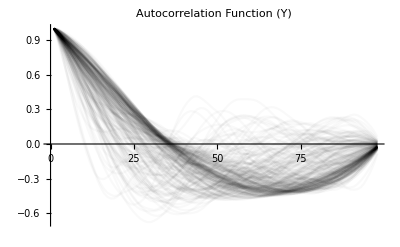

```mathematica
ListPlot[acfY,Joined->True,PlotStyle->Directive[Opacity[0.025],Black],
PlotLabel->Style["Autocorrelation Function (Y)",Bold,Black,FontSize->14],
AxesStyle-> {Thin,18}]
```

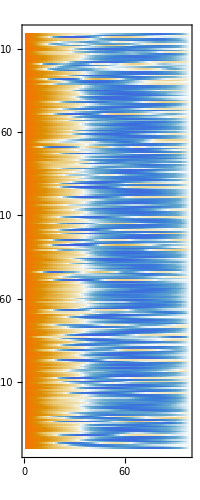

```mathematica
MatrixPlot[acfY,FrameTicks->{Range[10,250,50],Range[0,100,20]}]
```

## Experimental Trajectories

## Simulation compared with Experimental trajectories (The motion is convective)

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\Brachyury_motion_2.mx";
```

```mathematica
min=Min[Map[Length]@saved]
```

99

```mathematica
movAvg=MovingAverage[Take[#,min],2]&/@saved;
```

```mathematica
distDiff=Function[x,Prepend[Map[#-First@x&,Rest@x],{0,0}]]/@movAvg;
```

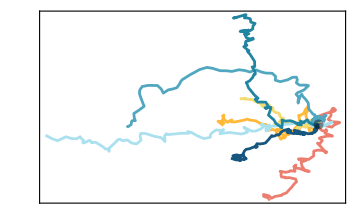

```mathematica
Show[
ListPlot[distDiff,Joined->True,PlotStyle->ColorData[24],ImageSize->Medium,Axes->False,Frame->True,FrameTicks->None,
PlotRange->All]/.AbsoluteThickness[_]:> AbsoluteThickness[2.0],
Graphics[{Opacity[0.4],Black,PointSize[0.02],Point@{0,0}}]]
```

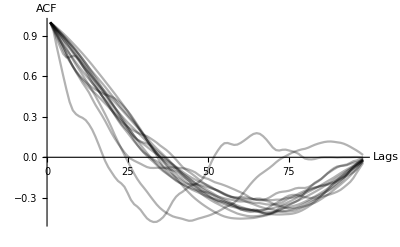

```mathematica
Block[{autocorrelation},
Show[
Map[x↦(
autocorrelation=CorrelationFunction[#,{0,Length@#-1}]&/@Transpose@movAvg[[x]];
ListLinePlot[autocorrelation,Joined->{True,True},PlotStyle->{{Opacity[0.3],Black},{Opacity[0.3],Black}}]),
Range@7],PlotRange-> All,BaseStyle->Directive[Thick,Opacity[0.7]],AxesLabel->{Style["Lags",{Bold,14}],
Style["ACF",{Bold,14}]},AxesStyle->Directive[Black, 12]
]
]
```

```mathematica
{acfExpX,acfExpY}=Transpose@Table[autocorrelation=CorrelationFunction[#,{0,Length@#-1}]&/@Transpose@movAvg[[x]],{x,7}];
```

```mathematica
xx=((Normal@GroupBy[Flatten[Thread[{Range[Length[#]],#}]&/@acfExpX,1],First-> Last,Mean])/. Rule-> List);
```

```mathematica
yy=((Normal@GroupBy[Flatten[Thread[{Range[Length[#]],#}]&/@acfExpY,1],First-> Last,Mean])/. Rule-> List);
```

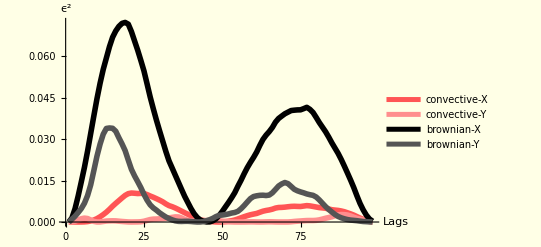

```mathematica
ListLinePlot[
MapThread[
MapThread[(Last[#1]-Last[#2])^2&,{((Normal@GroupBy[Flatten[Thread[{Range[Length[#]],#}]&/@#1,1],First-> Last,Mean])/. Rule-> List),
Thread[{Range[Length@First@#2],Mean[#2]}]}]&,{{acfExpX,acfExpY,acfExpX,acfExpY},{acfX,acfY,acfXr,acfYr}}],PlotStyle->{{Thickness[0.01],Lighter@Red},{Thickness[0.01],Nest[Lighter,Red,2]},{Thickness[0.01],Black},{Thickness[0.01],Lighter@Black}},
PlotLegends->{"convective-X","convective-Y","brownian-X","brownian-Y"},PlotRange->All,
AxesStyle->{{Thick,Black,16},{Thick,Black,16}},AxesLabel->{Style["Lags",Black],Style["ϵ^2",Bold,Black]},
Background->Lighter@LightYellow
]
```

```mathematica
(* Experimental trajectories with Brownian Motion *)
```

```mathematica
KolmogorovSmirnovTest[xx[[All,2]],Mean[acfXr],{"PValue","ShortTestConclusion"},SignificanceLevel->(0.01)]
```

{7.37492×10^-9,Reject}

```mathematica
KolmogorovSmirnovTest[yy[[All,2]],Mean[acfYr],{"PValue","ShortTestConclusion"},SignificanceLevel->(0.01)]
```

{0.000012526,Reject}

```mathematica
(* Experimental trajectories with simulated Fractional Brownian Motion *)
```

```mathematica
KolmogorovSmirnovTest[xx[[All,2]],Mean[acfX],{"PValue","ShortTestConclusion"},SignificanceLevel->(0.01)]
```

{0.00111001,Reject}

```mathematica
KolmogorovSmirnovTest[yy[[All,2]],Mean[acfY],{"PValue","ShortTestConclusion"},SignificanceLevel->(0.01)]
```

{0.993445,Do not reject}